

```mathematica
Plot[x,{x,-2,2}]
```

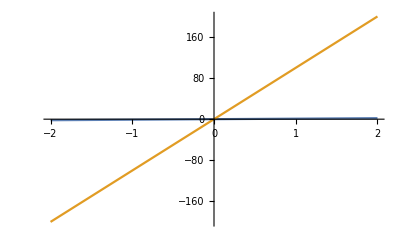

```mathematica
Plot[{x,100x},{x,-2,2}]
```

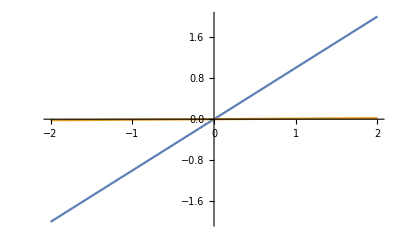

```mathematica
Plot[{x,x/100},{x,-2,2}]
```

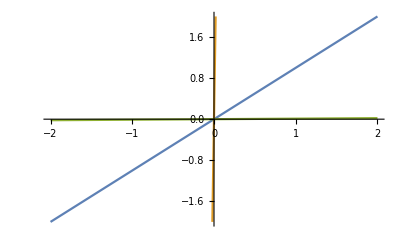

```mathematica
Plot[{x,100x,x/100},{x,-2,2},PlotRange->{-2,2}]
```

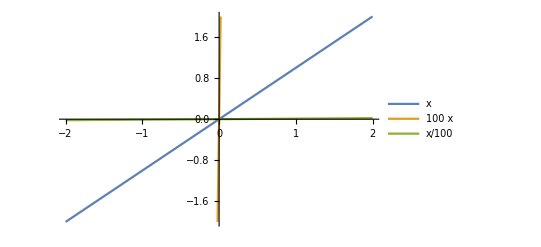

```mathematica
Plot[{x,100x,x/100},{x,-2,2},PlotRange->{-2,2},PlotLegends->"Expressions"]
```

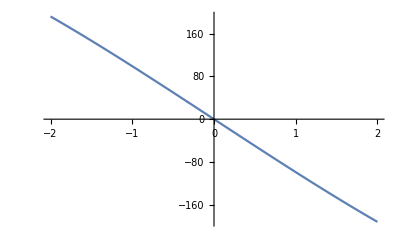

```mathematica
Plot[x^3-100x,{x,-2,2}]
```

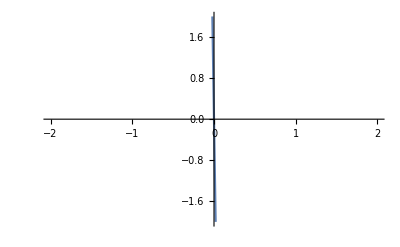

```mathematica
Plot[x^3-100x,{x,-2,2},PlotRange->{-2,2}]
```

```mathematica
Plot[x^3-100x,{x,-2,2}]
```

-Graphics-

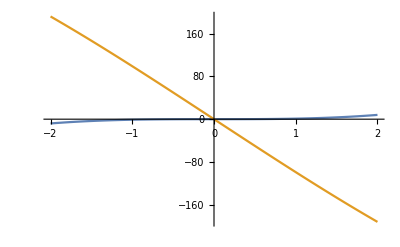

```mathematica
Plot[{x^3,x^3-100x},{x,-2,2}]
```

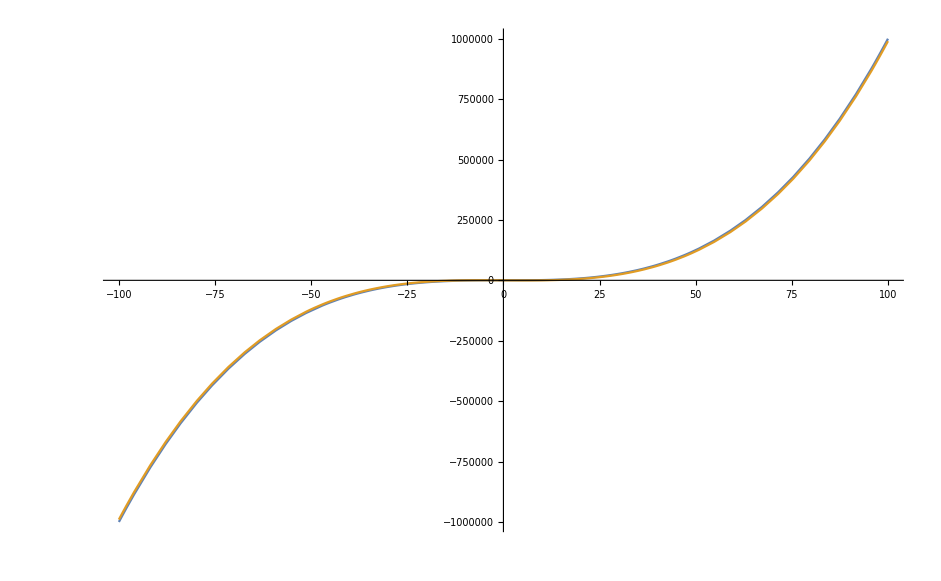

```mathematica
Plot[{x^3,x^3-100x},{x,-100,100},PlotRange->Full]
```

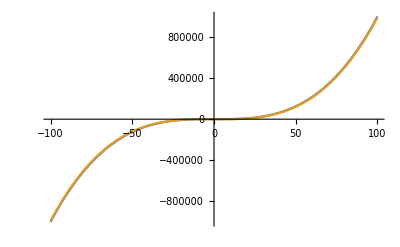

```mathematica
Plot[{x^3-1,x^3-100x},{x,-100,100},PlotRange->Full]
```

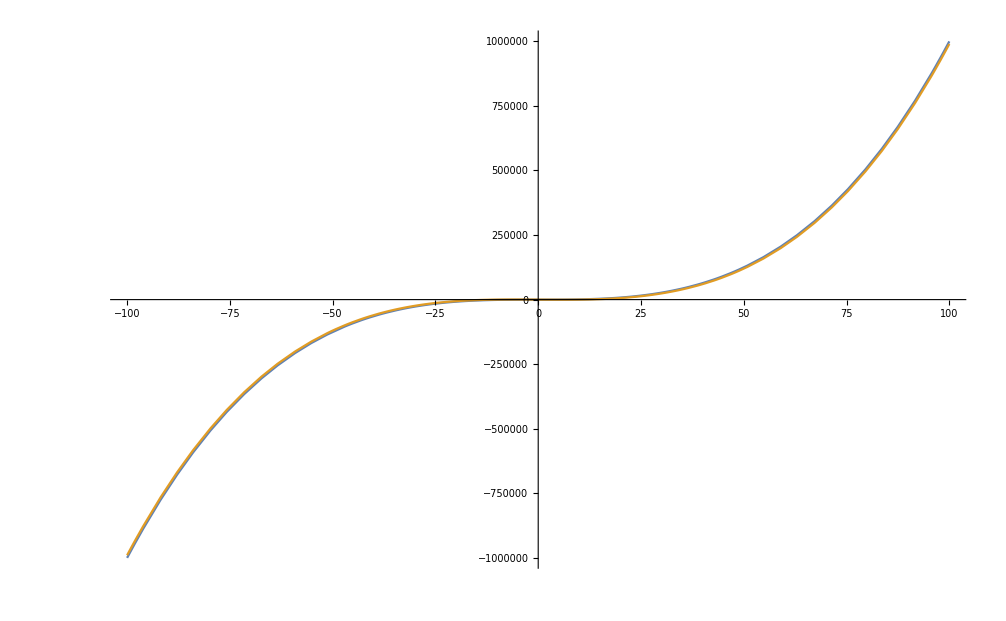

```mathematica
Plot[{x^3-100,x^3-100x},{x,-100,100},PlotRange->Full]
```

```mathematica
ArcCurvature[x^3-a x,x]
```

6 √(1/((1+a^2-6 a x^2+9 x^4)^3)) Abs[x]

```mathematica
Manipulate[Plot[6 √(1/((1+a^2-6 a x^2+9 x^4)^3)) Abs[x],{x,-0.7964190845067556,0.7964190845067556}],{a,-1.0949962496114323,1.0949962496114323}]
```

```mathematica
Plot3D[6 √(1/((1+a^2-6 a x^2+9 x^4)^3)) Abs[x],{x,-3,3},{a,0,100}]
```

-Graphics3D-

```mathematica
Plot3D[6 √(1/((1+a^2-6 a x^2+9 x^4)^3)) Abs[x],{x,-3,3},{a,0,100},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
D[f[x]/g[x],x]
```

f'[x]/g[x]-(f[x] g'[x])/g[x]^2

```mathematica
D[f[x]/(√(1+g[x])),x]
```

f'[x]/(√(1+g[x]))-(f[x] g'[x])/(2 (1+g[x])^(3/2))

```mathematica
Plot3D[6 √(1/((1+a^2-6 a x^2+9 x^4)^3)) Abs[x],{x,-3,3},{a,0,100},AxesLabel->Automatic,PlotRange->Full]
```

-Graphics3D-

```mathematica
FindMaximum[{6 √(1/((1+a^2-6 a x^2+9 x^4)^3)) Abs[x],-3≤x≤3,0<a≤50},{x,y}]
```

FindMaximum[{6 √(1/((1+a^2-6 a x^2+9 x^4)^3)) Abs[x],-3≤x≤3,0<a≤50},{x,y}]

```mathematica
FindMaximum[{6 √(1/((1+a^2-6 a x^2+9 x^4)^3)) Abs[x],-3≤x≤3,0<a≤50},{x,a}]
```

{18.,{x→3.,a→27.}}

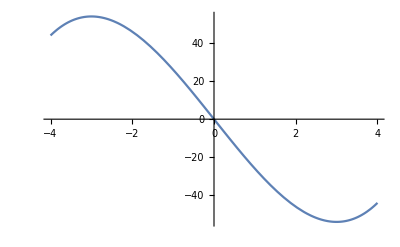

```mathematica
Plot[x^3-27x,{x,-4,4}]
```

```mathematica
FindMaximum[{6 √(1/((1+a^2-6 a x^2+9 x^4)^3)) Abs[x],-4≤x≤4,0<a≤50},{x,a}]
```

{24.,{x→4.,a→48.}}

```mathematica
Series[Sin[x],{x,0,10}]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11

```mathematica
Normal[x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880

```mathematica
ArcCurvature[{x,x-x^3/6+x^5/120-x^7/5040+x^9/362880},x]
```

(13005619200 Abs[x] Abs[-5040+840 x^2-42 x^4+x^6])/((3251404800-1625702400 x^2+541900800 x^4-72253440 x^6+5160960 x^8-228480 x^10+6496 x^12-112 x^14+x^16)^(3/2))

```mathematica
FullSimplify[ArcCurvature[{x,x-x^3/6+x^5/120-x^7/5040+x^9/362880},x],x∈Reals]
```

(13005619200 Abs[x] Abs[-5040+840 x^2-42 x^4+x^6])/((3251404800+x^2 (-20160+1680 x^2-56 x^4+x^6) (80640-20160 x^2+1680 x^4-56 x^6+x^8))^(3/2))

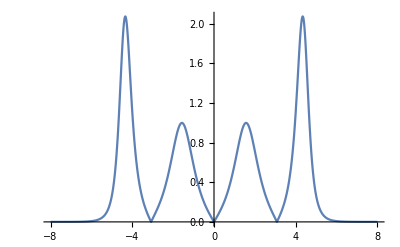

```mathematica
Plot[(13005619200 Abs[x] Abs[-5040+840 x^2-42 x^4+x^6])/((3251404800+x^2 (-20160+1680 x^2-56 x^4+x^6) (80640-20160 x^2+1680 x^4-56 x^6+x^8))^(3/2)),{x,-8,8}]
```

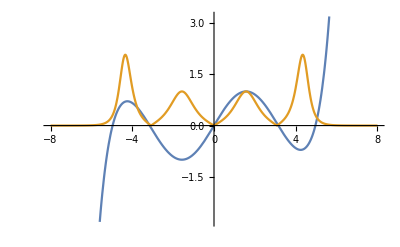

```mathematica
Plot[{x-x^3/6+x^5/120-x^7/5040+x^9/362880,(13005619200 Abs[x] Abs[-5040+840 x^2-42 x^4+x^6])/((3251404800+x^2 (-20160+1680 x^2-56 x^4+x^6) (80640-20160 x^2+1680 x^4-56 x^6+x^8))^(3/2))},{x,-8,8}]
```

```mathematica
(13005619200 Abs[x] Abs[-5040+840 x^2-42 x^4+x^6])/((3251404800-1625702400 x^2+541900800 x^4-72253440 x^6+5160960 x^8-228480 x^10+6496 x^12-112 x^14+x^16)^(3/2))
```

(13005619200 Abs[x] Abs[-5040+840 x^2-42 x^4+x^6])/((3251404800-1625702400 x^2+541900800 x^4-72253440 x^6+5160960 x^8-228480 x^10+6496 x^12-112 x^14+x^16)^(3/2))

```mathematica
Plot[(13005619200 Abs[x] Abs[-5040+840 x^2-42 x^4+x^6])/((3251404800-1625702400 x^2+541900800 x^4-72253440 x^6+5160960 x^8-228480 x^10+6496 x^12-112 x^14+x^16)^(3/2)),{x,-8,8}]
```

-Graphics-

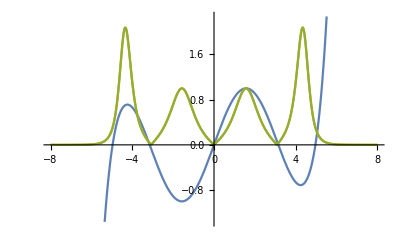

```mathematica
Plot[{x-x^3/6+x^5/120-x^7/5040+x^9/362880,(13005619200 Abs[x] Abs[-5040+840 x^2-42 x^4+x^6])/((3251404800+x^2 (-20160+1680 x^2-56 x^4+x^6) (80640-20160 x^2+1680 x^4-56 x^6+x^8))^(3/2)),(13005619200 Abs[x] Abs[-5040+840 x^2-42 x^4+x^6])/((3251404800-1625702400 x^2+541900800 x^4-72253440 x^6+5160960 x^8-228480 x^10+6496 x^12-112 x^14+x^16)^(3/2))},{x,-8,8}]
```

```mathematica
Manipulate[
With[{f=Function[x,Normal[Series[Sin[x],{x,0,10}]]]},
f[x]
],{a,0,20,1}]
```

```mathematica
Manipulate[
With[{f=Function[x,Normal[Series[Sin[x],{x,0,a}]]]},
f[x]
],{a,0,20,1}]
```

```mathematica
Manipulate[
With[{f=Function[x,Normal[Series[Sin[x],{x,0,a}]]]},
Plot[{f[x],ArcCurvature[{x,f[x]},x]},{x,-10,10}]
],{a,0,20,1}]
```

General::ivar: -9.99959 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

ArcCurvature::ivar: -9.99959 is not a valid variable.

ArcCurvature::ivar: -9.59143 is not a valid variable.

General::stop: Further output of ArcCurvature::ivar will be suppressed during this calculation.

General::ivar: -9.99959 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

ArcCurvature::ivar: -9.99959 is not a valid variable.

ArcCurvature::ivar: -9.59143 is not a valid variable.

General::stop: Further output of ArcCurvature::ivar will be suppressed during this calculation.

```mathematica
Manipulate[
With[{f=Function[x,Normal[Series[Sin[x],{x,0,a}]]]},
FullSimplify[ArcCurvature[{x,f[x]},x],Element[x,Reals]]
],{a,0,20,1}]
```

```mathematica
Table[
With[{f=Function[x,Normal[Series[Sin[x],{x,0,a}]]]},
FullSimplify[ArcCurvature[{x,f[x]},x],Element[x,Reals]]
],{a,0,20,1}]
```

{0,0,0,(8 Abs[x])/((8-4 x^2+x^4)^(3/2)),(8 Abs[x])/((8-4 x^2+x^4)^(3/2)),(2304 Abs[x] Abs[-6+x^2])/((1152+x^2 (-12+x^2) (48-12 x^2+x^4))^(3/2)),(2304 Abs[x] Abs[-6+x^2])/((1152+x^2 (-12+x^2) (48-12 x^2+x^4))^(3/2)),(3110400 (120-20 x^2+x^4) Abs[x])/((1036800+x^2 (360-30 x^2+x^4) (-1440+360 x^2-30 x^4+x^6))^(3/2)),(3110400 (120-20 x^2+x^4) Abs[x])/((1036800+x^2 (360-30 x^2+x^4) (-1440+360 x^2-30 x^4+x^6))^(3/2)),(13005619200 Abs[x] Abs[-5040+840 x^2-42 x^4+x^6])/((3251404800+x^2 (-20160+1680 x^2-56 x^4+x^6) (80640-20160 x^2+1680 x^4-56 x^6+x^8))^(3/2)),(13005619200 Abs[x] Abs[-5040+840 x^2-42 x^4+x^6])/((3251404800+x^2 (-20160+1680 x^2-56 x^4+x^6) (80640-20160 x^2+1680 x^4-56 x^6+x^8))^(3/2)),(131681894400000 Abs[x] Abs[362880-60480 x^2+3024 x^4-72 x^6+x^8])/((26336378880000+x^2 (1814400-151200 x^2+5040 x^4-90 x^6+x^8) (-7257600+1814400 x^2-151200 x^4+5040 x^6-90 x^8+x^10))^(3/2)),(131681894400000 Abs[x] Abs[362880-60480 x^2+3024 x^4-72 x^6+x^8])/((26336378880000+x^2 (1814400-151200 x^2+5040 x^4-90 x^6+x^8) (-7257600+1814400 x^2-151200 x^4+5040 x^6-90 x^8+x^10))^(3/2)),(2753310393630720000 Abs[x] Abs[-39916800+6652800 x^2-332640 x^4+7920 x^6-110 x^8+x^10])/((458885065605120000+x^2 (-239500800+19958400 x^2-665280 x^4+11880 x^6-132 x^8+x^10) (958003200-239500800 x^2+19958400 x^4-665280 x^6+11880 x^8-132 x^10+x^12))^(3/2)),(2753310393630720000 Abs[x] Abs[-39916800+6652800 x^2-332640 x^4+7920 x^6-110 x^8+x^10])/((458885065605120000+x^2 (-239500800+19958400 x^2-665280 x^4+11880 x^6-132 x^8+x^10) (958003200-239500800 x^2+19958400 x^4-665280 x^6+11880 x^8-132 x^10+x^12))^(3/2)),106400762391727964160000 √(1/(15200108913103994880000+x^2 (43589145600-3632428800 x^2+121080960 x^4-2162160 x^6+24024 x^8-182 x^10+x^12) (-174356582400+43589145600 x^2-3632428800 x^4+121080960 x^6-2162160 x^8+24024 x^10-182 x^12+x^14))^3) Abs[x] Abs[6227020800-1037836800 x^2+51891840 x^4-1235520 x^6+17160 x^8-156 x^10+x^12],106400762391727964160000 √(1/(15200108913103994880000+x^2 (43589145600-3632428800 x^2+121080960 x^4-2162160 x^6+24024 x^8-182 x^10+x^12) (-174356582400+43589145600 x^2-3632428800 x^4+121080960 x^6-2162160 x^8+24024 x^10-182 x^12+x^14))^3) Abs[x] Abs[6227020800-1037836800 x^2+51891840 x^4-1235520 x^6+17160 x^8-156 x^10+x^12],7004210187158320840704000000 √(1/(875526273394790105088000000+x^2 (-10461394944000+871782912000 x^2-29059430400 x^4+518918400 x^6-5765760 x^8+43680 x^10-240 x^12+x^14) (41845579776000-10461394944000 x^2+871782912000 x^4-29059430400 x^6+518918400 x^8-5765760 x^10+43680 x^12-240 x^14+x^16))^3) Abs[x] Abs[-1307674368000+217945728000 x^2-10897286400 x^4+259459200 x^6-3603600 x^8+32760 x^10-210 x^12+x^14],7004210187158320840704000000 √(1/(875526273394790105088000000+x^2 (-10461394944000+871782912000 x^2-29059430400 x^4+518918400 x^6-5765760 x^8+43680 x^10-240 x^12+x^14) (41845579776000-10461394944000 x^2+871782912000 x^4-29059430400 x^6+518918400 x^8-5765760 x^10+43680 x^12-240 x^14+x^16))^3) Abs[x] Abs[-1307674368000+217945728000 x^2-10897286400 x^4+259459200 x^6-3603600 x^8+32760 x^10-210 x^12+x^14],737827003220351096520179712000000 √(1/(81980778135594566280019968000000+x^2 (3201186852864000-266765571072000 x^2+8892185702400 x^4-158789030400 x^6+1764322560 x^8-13366080 x^10+73440 x^12-306 x^14+x^16) (-12804747411456000+3201186852864000 x^2-266765571072000 x^4+8892185702400 x^6-158789030400 x^8+1764322560 x^10-13366080 x^12+73440 x^14-306 x^16+x^18))^3) Abs[x] Abs[355687428096000-59281238016000 x^2+2964061900800 x^4-70572902400 x^6+980179200 x^8-8910720 x^10+57120 x^12-272 x^14+x^16],737827003220351096520179712000000 √(1/(81980778135594566280019968000000+x^2 (3201186852864000-266765571072000 x^2+8892185702400 x^4-158789030400 x^6+1764322560 x^8-13366080 x^10+73440 x^12-306 x^14+x^16) (-12804747411456000+3201186852864000 x^2-266765571072000 x^4+8892185702400 x^6-158789030400 x^8+1764322560 x^10-13366080 x^12+73440 x^14-306 x^16+x^18))^3) Abs[x] Abs[355687428096000-59281238016000 x^2+2964061900800 x^4-70572902400 x^6+980179200 x^8-8910720 x^10+57120 x^12-272 x^14+x^16]}

```mathematica
Table[
With[{f=Function[x,Normal[Series[Sin[x],{x,0,a}]]]},
f[x]
],{a,0,20,1}]
```

{0,x,x,x-x^3/6,x-x^3/6,x-x^3/6+x^5/120,x-x^3/6+x^5/120,x-x^3/6+x^5/120-x^7/5040,x-x^3/6+x^5/120-x^7/5040,x-x^3/6+x^5/120-x^7/5040+x^9/362880,x-x^3/6+x^5/120-x^7/5040+x^9/362880,x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800,x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800,x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800,x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800,x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000,x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000,x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000+x^17/355687428096000,x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000+x^17/355687428096000,x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000+x^17/355687428096000-x^19/121645100408832000,x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000+x^17/355687428096000-x^19/121645100408832000}

```mathematica
Transpose[{Out[38],Out[39]}]
```

{{0,0},{0,x},{0,x},{(8 Abs[x])/((8-4 x^2+x^4)^(3/2)),x-x^3/6},{(8 Abs[x])/((8-4 x^2+x^4)^(3/2)),x-x^3/6},{(2304 Abs[x] Abs[-6+x^2])/((1152+x^2 (-12+x^2) (48-12 x^2+x^4))^(3/2)),x-x^3/6+x^5/120},{(2304 Abs[x] Abs[-6+x^2])/((1152+x^2 (-12+x^2) (48-12 x^2+x^4))^(3/2)),x-x^3/6+x^5/120},{(3110400 (120-20 x^2+x^4) Abs[x])/((1036800+x^2 (360-30 x^2+x^4) (-1440+360 x^2-30 x^4+x^6))^(3/2)),x-x^3/6+x^5/120-x^7/5040},{(3110400 (120-20 x^2+x^4) Abs[x])/((1036800+x^2 (360-30 x^2+x^4) (-1440+360 x^2-30 x^4+x^6))^(3/2)),x-x^3/6+x^5/120-x^7/5040},{(13005619200 Abs[x] Abs[-5040+840 x^2-42 x^4+x^6])/((3251404800+x^2 (-20160+1680 x^2-56 x^4+x^6) (80640-20160 x^2+1680 x^4-56 x^6+x^8))^(3/2)),x-x^3/6+x^5/120-x^7/5040+x^9/362880},{(13005619200 Abs[x] Abs[-5040+840 x^2-42 x^4+x^6])/((3251404800+x^2 (-20160+1680 x^2-56 x^4+x^6) (80640-20160 x^2+1680 x^4-56 x^6+x^8))^(3/2)),x-x^3/6+x^5/120-x^7/5040+x^9/362880},{(131681894400000 Abs[x] Abs[362880-60480 x^2+3024 x^4-72 x^6+x^8])/((26336378880000+x^2 (1814400-151200 x^2+5040 x^4-90 x^6+x^8) (-7257600+1814400 x^2-151200 x^4+5040 x^6-90 x^8+x^10))^(3/2)),x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800},{(131681894400000 Abs[x] Abs[362880-60480 x^2+3024 x^4-72 x^6+x^8])/((26336378880000+x^2 (1814400-151200 x^2+5040 x^4-90 x^6+x^8) (-7257600+1814400 x^2-151200 x^4+5040 x^6-90 x^8+x^10))^(3/2)),x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800},{(2753310393630720000 Abs[x] Abs[-39916800+6652800 x^2-332640 x^4+7920 x^6-110 x^8+x^10])/((458885065605120000+x^2 (-239500800+19958400 x^2-665280 x^4+11880 x^6-132 x^8+x^10) (958003200-239500800 x^2+19958400 x^4-665280 x^6+11880 x^8-132 x^10+x^12))^(3/2)),x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800},{(2753310393630720000 Abs[x] Abs[-39916800+6652800 x^2-332640 x^4+7920 x^6-110 x^8+x^10])/((458885065605120000+x^2 (-239500800+19958400 x^2-665280 x^4+11880 x^6-132 x^8+x^10) (958003200-239500800 x^2+19958400 x^4-665280 x^6+11880 x^8-132 x^10+x^12))^(3/2)),x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800},{106400762391727964160000 √(1/(15200108913103994880000+x^2 (43589145600-3632428800 x^2+121080960 x^4-2162160 x^6+24024 x^8-182 x^10+x^12) (-174356582400+43589145600 x^2-3632428800 x^4+121080960 x^6-2162160 x^8+24024 x^10-182 x^12+x^14))^3) Abs[x] Abs[6227020800-1037836800 x^2+51891840 x^4-1235520 x^6+17160 x^8-156 x^10+x^12],x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000},{106400762391727964160000 √(1/(15200108913103994880000+x^2 (43589145600-3632428800 x^2+121080960 x^4-2162160 x^6+24024 x^8-182 x^10+x^12) (-174356582400+43589145600 x^2-3632428800 x^4+121080960 x^6-2162160 x^8+24024 x^10-182 x^12+x^14))^3) Abs[x] Abs[6227020800-1037836800 x^2+51891840 x^4-1235520 x^6+17160 x^8-156 x^10+x^12],x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000},{7004210187158320840704000000 √(1/(875526273394790105088000000+x^2 (-10461394944000+871782912000 x^2-29059430400 x^4+518918400 x^6-5765760 x^8+43680 x^10-240 x^12+x^14) (41845579776000-10461394944000 x^2+871782912000 x^4-29059430400 x^6+518918400 x^8-5765760 x^10+43680 x^12-240 x^14+x^16))^3) Abs[x] Abs[-1307674368000+217945728000 x^2-10897286400 x^4+259459200 x^6-3603600 x^8+32760 x^10-210 x^12+x^14],x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000+x^17/355687428096000},{7004210187158320840704000000 √(1/(875526273394790105088000000+x^2 (-10461394944000+871782912000 x^2-29059430400 x^4+518918400 x^6-5765760 x^8+43680 x^10-240 x^12+x^14) (41845579776000-10461394944000 x^2+871782912000 x^4-29059430400 x^6+518918400 x^8-5765760 x^10+43680 x^12-240 x^14+x^16))^3) Abs[x] Abs[-1307674368000+217945728000 x^2-10897286400 x^4+259459200 x^6-3603600 x^8+32760 x^10-210 x^12+x^14],x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000+x^17/355687428096000},{737827003220351096520179712000000 √(1/(81980778135594566280019968000000+x^2 (3201186852864000-266765571072000 x^2+8892185702400 x^4-158789030400 x^6+1764322560 x^8-13366080 x^10+73440 x^12-306 x^14+x^16) (-12804747411456000+3201186852864000 x^2-266765571072000 x^4+8892185702400 x^6-158789030400 x^8+1764322560 x^10-13366080 x^12+73440 x^14-306 x^16+x^18))^3) Abs[x] Abs[355687428096000-59281238016000 x^2+2964061900800 x^4-70572902400 x^6+980179200 x^8-8910720 x^10+57120 x^12-272 x^14+x^16],x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000+x^17/355687428096000-x^19/121645100408832000},{737827003220351096520179712000000 √(1/(81980778135594566280019968000000+x^2 (3201186852864000-266765571072000 x^2+8892185702400 x^4-158789030400 x^6+1764322560 x^8-13366080 x^10+73440 x^12-306 x^14+x^16) (-12804747411456000+3201186852864000 x^2-266765571072000 x^4+8892185702400 x^6-158789030400 x^8+1764322560 x^10-13366080 x^12+73440 x^14-306 x^16+x^18))^3) Abs[x] Abs[355687428096000-59281238016000 x^2+2964061900800 x^4-70572902400 x^6+980179200 x^8-8910720 x^10+57120 x^12-272 x^14+x^16],x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000+x^17/355687428096000-x^19/121645100408832000}}

```mathematica
Manipulate[
Plot[a,{x,-3,3}],
{a,Transpose[{Out[38],Out[39]}]}]
```

```mathematica
Transpose[{Out[38],Out[39]}]
```

{{0,0},{0,x},{0,x},{(8 Abs[x])/((8-4 x^2+x^4)^(3/2)),x-x^3/6},{(8 Abs[x])/((8-4 x^2+x^4)^(3/2)),x-x^3/6},{(2304 Abs[x] Abs[-6+x^2])/((1152+x^2 (-12+x^2) (48-12 x^2+x^4))^(3/2)),x-x^3/6+x^5/120},{(2304 Abs[x] Abs[-6+x^2])/((1152+x^2 (-12+x^2) (48-12 x^2+x^4))^(3/2)),x-x^3/6+x^5/120},{(3110400 (120-20 x^2+x^4) Abs[x])/((1036800+x^2 (360-30 x^2+x^4) (-1440+360 x^2-30 x^4+x^6))^(3/2)),x-x^3/6+x^5/120-x^7/5040},{(3110400 (120-20 x^2+x^4) Abs[x])/((1036800+x^2 (360-30 x^2+x^4) (-1440+360 x^2-30 x^4+x^6))^(3/2)),x-x^3/6+x^5/120-x^7/5040},{(13005619200 Abs[x] Abs[-5040+840 x^2-42 x^4+x^6])/((3251404800+x^2 (-20160+1680 x^2-56 x^4+x^6) (80640-20160 x^2+1680 x^4-56 x^6+x^8))^(3/2)),x-x^3/6+x^5/120-x^7/5040+x^9/362880},{(13005619200 Abs[x] Abs[-5040+840 x^2-42 x^4+x^6])/((3251404800+x^2 (-20160+1680 x^2-56 x^4+x^6) (80640-20160 x^2+1680 x^4-56 x^6+x^8))^(3/2)),x-x^3/6+x^5/120-x^7/5040+x^9/362880},{(131681894400000 Abs[x] Abs[362880-60480 x^2+3024 x^4-72 x^6+x^8])/((26336378880000+x^2 (1814400-151200 x^2+5040 x^4-90 x^6+x^8) (-7257600+1814400 x^2-151200 x^4+5040 x^6-90 x^8+x^10))^(3/2)),x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800},{(131681894400000 Abs[x] Abs[362880-60480 x^2+3024 x^4-72 x^6+x^8])/((26336378880000+x^2 (1814400-151200 x^2+5040 x^4-90 x^6+x^8) (-7257600+1814400 x^2-151200 x^4+5040 x^6-90 x^8+x^10))^(3/2)),x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800},{(2753310393630720000 Abs[x] Abs[-39916800+6652800 x^2-332640 x^4+7920 x^6-110 x^8+x^10])/((458885065605120000+x^2 (-239500800+19958400 x^2-665280 x^4+11880 x^6-132 x^8+x^10) (958003200-239500800 x^2+19958400 x^4-665280 x^6+11880 x^8-132 x^10+x^12))^(3/2)),x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800},{(2753310393630720000 Abs[x] Abs[-39916800+6652800 x^2-332640 x^4+7920 x^6-110 x^8+x^10])/((458885065605120000+x^2 (-239500800+19958400 x^2-665280 x^4+11880 x^6-132 x^8+x^10) (958003200-239500800 x^2+19958400 x^4-665280 x^6+11880 x^8-132 x^10+x^12))^(3/2)),x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800},{106400762391727964160000 √(1/(15200108913103994880000+x^2 (43589145600-3632428800 x^2+121080960 x^4-2162160 x^6+24024 x^8-182 x^10+x^12) (-174356582400+43589145600 x^2-3632428800 x^4+121080960 x^6-2162160 x^8+24024 x^10-182 x^12+x^14))^3) Abs[x] Abs[6227020800-1037836800 x^2+51891840 x^4-1235520 x^6+17160 x^8-156 x^10+x^12],x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000},{106400762391727964160000 √(1/(15200108913103994880000+x^2 (43589145600-3632428800 x^2+121080960 x^4-2162160 x^6+24024 x^8-182 x^10+x^12) (-174356582400+43589145600 x^2-3632428800 x^4+121080960 x^6-2162160 x^8+24024 x^10-182 x^12+x^14))^3) Abs[x] Abs[6227020800-1037836800 x^2+51891840 x^4-1235520 x^6+17160 x^8-156 x^10+x^12],x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000},{7004210187158320840704000000 √(1/(875526273394790105088000000+x^2 (-10461394944000+871782912000 x^2-29059430400 x^4+518918400 x^6-5765760 x^8+43680 x^10-240 x^12+x^14) (41845579776000-10461394944000 x^2+871782912000 x^4-29059430400 x^6+518918400 x^8-5765760 x^10+43680 x^12-240 x^14+x^16))^3) Abs[x] Abs[-1307674368000+217945728000 x^2-10897286400 x^4+259459200 x^6-3603600 x^8+32760 x^10-210 x^12+x^14],x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000+x^17/355687428096000},{7004210187158320840704000000 √(1/(875526273394790105088000000+x^2 (-10461394944000+871782912000 x^2-29059430400 x^4+518918400 x^6-5765760 x^8+43680 x^10-240 x^12+x^14) (41845579776000-10461394944000 x^2+871782912000 x^4-29059430400 x^6+518918400 x^8-5765760 x^10+43680 x^12-240 x^14+x^16))^3) Abs[x] Abs[-1307674368000+217945728000 x^2-10897286400 x^4+259459200 x^6-3603600 x^8+32760 x^10-210 x^12+x^14],x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000+x^17/355687428096000},{737827003220351096520179712000000 √(1/(81980778135594566280019968000000+x^2 (3201186852864000-266765571072000 x^2+8892185702400 x^4-158789030400 x^6+1764322560 x^8-13366080 x^10+73440 x^12-306 x^14+x^16) (-12804747411456000+3201186852864000 x^2-266765571072000 x^4+8892185702400 x^6-158789030400 x^8+1764322560 x^10-13366080 x^12+73440 x^14-306 x^16+x^18))^3) Abs[x] Abs[355687428096000-59281238016000 x^2+2964061900800 x^4-70572902400 x^6+980179200 x^8-8910720 x^10+57120 x^12-272 x^14+x^16],x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000+x^17/355687428096000-x^19/121645100408832000},{737827003220351096520179712000000 √(1/(81980778135594566280019968000000+x^2 (3201186852864000-266765571072000 x^2+8892185702400 x^4-158789030400 x^6+1764322560 x^8-13366080 x^10+73440 x^12-306 x^14+x^16) (-12804747411456000+3201186852864000 x^2-266765571072000 x^4+8892185702400 x^6-158789030400 x^8+1764322560 x^10-13366080 x^12+73440 x^14-306 x^16+x^18))^3) Abs[x] Abs[355687428096000-59281238016000 x^2+2964061900800 x^4-70572902400 x^6+980179200 x^8-8910720 x^10+57120 x^12-272 x^14+x^16],x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000+x^17/355687428096000-x^19/121645100408832000}}

```mathematica
Manipulate[
Plot[a,{x,-3,3}],
{a,Out[40]}]
```

```mathematica
Manipulate[
Plot[{Sin[x],a}
,{x,-3,3}],
{a,Out[38]}]
```

```mathematica
Manipulate[
Plot[{Sin[x],a}
,{x,-10,10}],
{a,Out[38]}]
```

```mathematica
Abs[x]-f[x]==x
```

Abs[x]-f[x]==x

```mathematica
Reduce[Abs[x]-f[x]==x]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[Abs[x]-f[x]==x]

```mathematica
CoordinateChartData[]
```

{{{Bipolar,{a}},Euclidean,2},{{BipolarCylindrical,{a}},Euclidean,3},{{Bispherical,{a}},Euclidean,3},{Cartesian,Euclidean,1},{Cartesian,Euclidean,2},{Cartesian,Euclidean,3},{Cartesian,Euclidean,4},{Cartesian,Euclidean,5},{Cartesian,Euclidean,6},{Cartesian,Euclidean,7},{Cartesian,Euclidean,8},{Cartesian,Euclidean,9},{Cartesian,Euclidean,10},{CircularParabolic,Euclidean,3},{{Confocal,{α,β}},Euclidean,2},{{Confocal,{α,β,γ}},Euclidean,3},{{Confocal,{α_1,α_2,α_3,α_4}},Euclidean,4},{{Confocal,{α_1,α_2,α_3,α_4,α_5}},Euclidean,5},{{Confocal,{α_1,α_2,α_3,α_4,α_5,α_6}},Euclidean,6},{{Confocal,{α_1,α_2,α_3,α_4,α_5,α_6,α_7}},Euclidean,7},{{Confocal,{α_1,α_2,α_3,α_4,α_5,α_6,α_7,α_8}},Euclidean,8},{{Confocal,{α_1,α_2,α_3,α_4,α_5,α_6,α_7,α_8,α_9}},Euclidean,9},{{Confocal,{α_1,α_2,α_3,α_4,α_5,α_6,α_7,α_8,α_9,α_10}},Euclidean,10},{{Confocal,{α_1,α_2,α_3,α_4,α_5,α_6,α_7,α_8,α_9,α_10,α_11}},Euclidean,11},{{ConfocalParaboloidal,{α,β}},Euclidean,3},{{Conical,{b,c}},Euclidean,3},{Cylindrical,Euclidean,3},{{Elliptic,{a}},Euclidean,2},{{EllipticCylindrical,{a}},Euclidean,3},{Polar,Euclidean,2},{Hyperspherical,Euclidean,3},{Hyperspherical,Euclidean,4},{Hyperspherical,Euclidean,5},{Hyperspherical,Euclidean,6},{Hyperspherical,Euclidean,7},{Hyperspherical,Euclidean,8},{Hyperspherical,Euclidean,9},{Hyperspherical,Euclidean,10},{Hyperspherical,Euclidean,11},{{OblateSpheroidal,{a}},Euclidean,3},{ParabolicCylindrical,Euclidean,3},{PlanarParabolic,Euclidean,2},{{ProlateSpheroidal,{a}},Euclidean,3},{Spherical,Euclidean,3},{{Toroidal,{a}},Euclidean,3},{Standard,{Sphere,{R}},1},{Standard,{Sphere,{R}},2},{Standard,{Sphere,{R}},3},{Standard,{Sphere,{R}},4},{Standard,{Sphere,{R}},5},{Standard,{Sphere,{R}},6},{Standard,{Sphere,{R}},7},{Standard,{Sphere,{R}},8},{Standard,{Sphere,{R}},9},{Standard,{Sphere,{R}},10},{Stereographic,{Sphere,{R}},1},{Stereographic,{Sphere,{R}},2},{Stereographic,{Sphere,{R}},3},{Stereographic,{Sphere,{R}},4},{Stereographic,{Sphere,{R}},5},{Stereographic,{Sphere,{R}},6},{Stereographic,{Sphere,{R}},7},{Stereographic,{Sphere,{R}},8},{Stereographic,{Sphere,{R}},9},{Stereographic,{Sphere,{R}},10}}

```mathematica
1
```

1